```mathematica
K2meV=0.086173324 
Table[(0.5+x),{x,0,360}];
cOmega0=31.58754341976066
```

0.0861733

31.5875

```mathematica
(*Define a function that calculates the heat capacity using from an excitation spectrum - arguments: Temperature - No. of eigenvalues to include - anharmonic perturbation*)

ff[T_,n_,h_]:=SetPrecision[-K2meV*1.5*T*Log[Total[Exp[-2*cOmega0* Table[(0.5+x+h),{x,0,n}]/(K2meV*T)]]],20];
```

```mathematica
(*Harmonic heat capacity at 4000K (in meV/atom), calculated using 2000 eigenvalue (to use a reference when working out the percentage error) *)
hc=(-T*D[D[ff[T,2000,0],T],T])/.T->4000
```

0.128898759323746751

```mathematica
(*Error in the heat capacity at 4000K for different numbers of eigenvalues, with respect to 2000 eigenvalue reference calculation*)Table[{n,(((-T*D[D[ff[T,n,0],T],T])/.T->4000)-(-T*D[D[ff[T,2000,0],T],T])/.T->4000)*100/hc},{n,10,200,10}]//TableForm
```

10 | -72.243441287259889
20 | -33.040372261616553
30 | -11.10757814280809
40 | -3.090303028101987
50 | -0.764195844892068
60 | -0.174859493572492
70 | -0.037893517777092
80 | -0.007889427603628
90 | -0.001592893869378
100 | -0.000313888656463
110 | -0.000060646771108
120 | -0.00001152819528
130 | -2.161533816×10^-6
140 | -4.00577477×10^-7
150 | -7.3490475×10^-8
160 | -1.336466×10^-8
170 | -2.411721×10^-9
180 | -4.32236×10^-10
190 | -7.6994×10^-11
200 | -1.364×10^-11

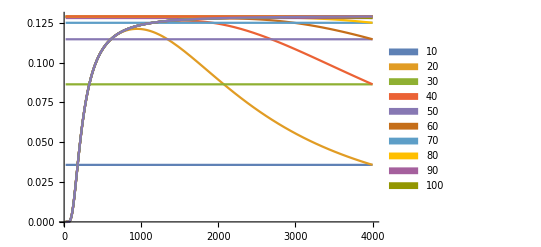

```mathematica
(*Convergence of harmonic heat capcity up to 4000K as a function of basis size*)
(*Harmonic heat capacity as as function of temperature based on a partition function evaluated at different numbers of eigenvectors*)
Plot[Evaluate@Table[{(-T*D[D[ff[T,n,0],T],T])/.T->4000,(-T*D[D[ff[T,n,0],T],T])/.T->t},{n,10,100,10}],{t,20,4000},PlotRange->All,PlotLegends->SwatchLegend[Table[i,{i,10,100,10}]]]
```

10 | -64.108336852519468
20 | -24.21452625594134
30 | -5.717215340954354
40 | -0.957677312869694
50 | -0.12294592557485
60 | -0.012614934708033
70 | -0.00105918125896
80 | -0.00007381903024
90 | -4.31021064×10^-6
100 | -2.121842×10^-7
110 | -8.846645×10^-9
120 | -3.13435×10^-10
130 | -9.46×10^-12
140 | -2.43×10^-13
150 | -5.×10^-15
160 | 8.×10^-16
170 | 9.×10^-16
180 | 9.×10^-16
190 | 9.×10^-16
200 | 9.×10^-16
210 | 9.×10^-16
220 | 9.×10^-16
230 | 9.×10^-16
240 | 9.×10^-16
250 | 0.
260 | 0.
270 | 0.
280 | 0.
290 | 0.
300 | 0.
310 | 0.
320 | 0.
330 | 0.
340 | 0.
350 | 0.
360 | 0.
370 | 0.
380 | 0.
390 | 0.
400 | 0.

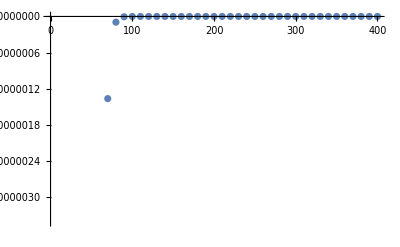

10 | -64.108336852519468
20 | -24.21452625594134
30 | -5.717215340954354
40 | -0.957677312869694
50 | -0.12294592557485
60 | -0.012614934708033
70 | -0.00105918125896
80 | -0.00007381903024
90 | -4.31021064×10^-6
100 | -2.121842×10^-7
110 | -8.846645×10^-9
120 | -3.13435×10^-10
130 | -9.46×10^-12
140 | -2.43×10^-13
150 | -5.×10^-15
160 | 8.×10^-16
170 | 9.×10^-16
180 | 9.×10^-16
190 | 9.×10^-16
200 | 9.×10^-16
210 | 9.×10^-16
220 | 9.×10^-16
230 | 9.×10^-16
240 | 9.×10^-16
250 | 0.
260 | 0.
270 | 0.
280 | 0.
290 | 0.
300 | 0.
310 | 0.
320 | 0.
330 | 0.
340 | 0.
350 | 0.
360 | 0.
370 | 0.
380 | 0.
390 | 0.
400 | 0.

-Graphics-

```mathematica
(*Error in the ANHARMONIC heat capacity at 4000K for different numbers of eigenvalues*)
(* ANHARMONIC spectrum -> 0.5 + x + x^2/250 *)
Table[{n,(((-T*D[D[ff[T,n,x*x/250],T],T])/.T->4000)-(-T*D[D[ff[T,2000,x*x/250],T],T])/.T->4000)*100/hc},{n,10,400,10}]//TableForm
ListPlot@Table[{n,((-T*D[D[ff[T,n,x*x/250],T],T])/.T->4000)-(-T*D[D[ff[T,2000,x*x/250],T],T])/.T->4000},{n,10,400,10}]
(* ANHARMONIC spectrum -> 0.5 + x + x^2/750 *)
Table[{n,(((-T*D[D[ff[T,n,x*x/250],T],T])/.T->4000)-(-T*D[D[ff[T,2000,x*x/250],T],T])/.T->4000)*100/hc},{n,10,400,10}]//TableForm
ListPlot@Table[{n,((-T*D[D[ff[T,n,x*x/250],T],T])/.T->4000)-(-T*D[D[ff[T,2000,x*x/250],T],T])/.T->4000},{n,10,400,10}]
```

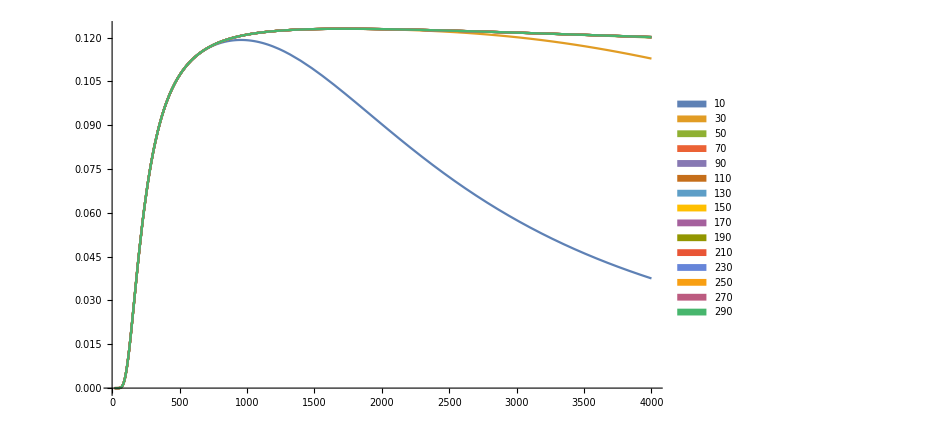

```mathematica
(*ANHarmonic heat capacity as as function of temperature based on a partition function evaluated at different numbers of eigenvectors*)
Plot[Evaluate@Table[{(-T*D[D[ff[T,n,x*x/250],T],T])/.T->t},{n,10,300,20}],{t,20,4000},PlotRange->All,PlotLegends->SwatchLegend[Flatten@Table[{i},{i,10,300,20}]],ImageSize->700]
```

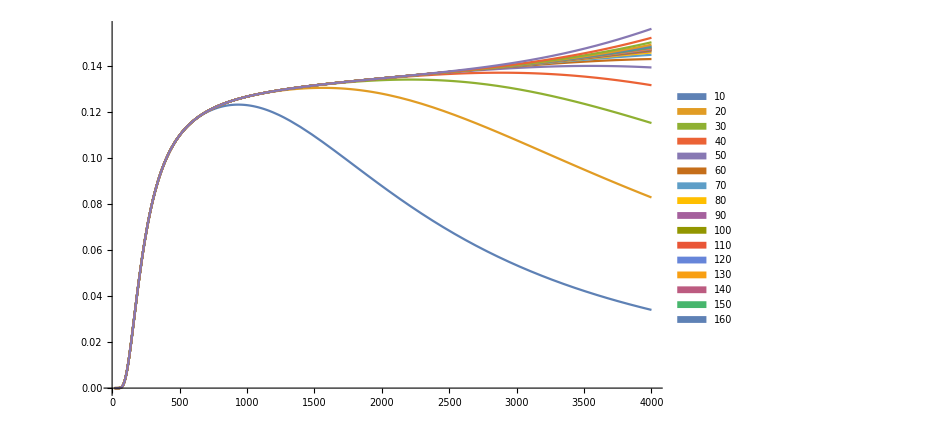

```mathematica
(*ANHarmonic heat capacity as as function of temperature based on a partition function evaluated at different numbers of eigenvectors*)
Plot[Evaluate@Table[{(-T*D[D[ff[T,n,-x*x/250],T],T])/.T->t},{n,10,200,10}],{t,20,4000},PlotRange->All,PlotLegends->SwatchLegend[Flatten@Table[{i},{i,10,200,10}]],ImageSize->700]
```